```mathematica
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/pulsation/toymodels

```mathematica
d𝒞dt = (-μC +eH pCH^(-1/4)aH (ωH H)/(1 + ωH ThH H + ωU ThU U) + eU pCU^(-1/4)aU (ωU U)/(1 + ωU ThU U + ωH ThH H) )𝒞;
dHdt = (-μH + rH (1 - H/𝒦) )H- pCH^(-1/4)aH  (ωH  H)/(1 + ωH ThH H + ωU ThU U) 𝒞;
dUdt = -ν U - pCU^(-1/4)aU (ωU U)/(1 + ωU ThU U + ωH ThH H) 𝒞 ;
```

```mathematica
Manipulate[Plot3D[(ωH H)/(h0 + ωH ThH H + ωU ThU U),{H, 0, 2}, {U, 0, 10}, AxesLabel->{"H", "U", "f(H, U)"} ],{ωH, 0.001, 3}, {h0, 0.001, 3}, {ThH, 0.001, 2}, {ThU, 0.001, 2}, {ωU, 0.001, 3}]
```

```mathematica
{pCH^(-1/4), pCU^(-1/4)}/.partestall
```

{0.955443,1.49535}

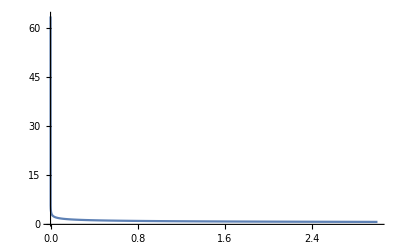

```mathematica
Plot[x^(-1/4), {x, 0, 3}, PlotRange->All]
```

```mathematica
sys = {d𝒞dt, dHdt, dUdt};
vars = {𝒞, H, U};
varst = {𝒞[t], H[t], U[t]};
```

```mathematica
partestall = {μC -> 0.01, μH -> 0.01, eH -> 0.3, aH -> 1, pCH -> 1.2, ωH -> 0.2,  ThH -> 1, ThU -> 0.1, ωU -> 0.3, eU -> 0.3, pCU -> 0.2,aU -> 0.1,  rH -> 0.5, 𝒦 -> 10, ν -> 0.1, δ -> 0.01};
```

```mathematica
sysNDSolve = MakeSystem[vars, t, sys];
init0 = {𝒞[0] == 0.1, H[0] == 0.21, U[0] == 0};
init1 = {𝒞[0] == 0.1, H[0] == 0.21, U[0] == 1.5};
init2 = {𝒞[0] == 0.1, H[0] == 0.21, U[0] == 0.5};
```

NDSolve::ndsz: At t == 248.752, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-2.23089×10^34,7.43629×10^34,0.}

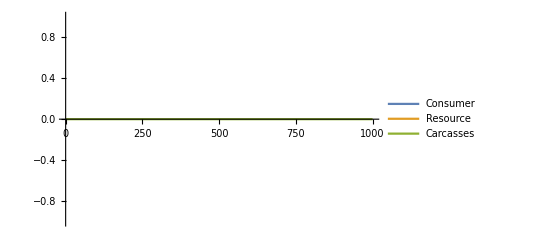

```mathematica
Tmax = 1000;
NDsolution = NDSolve[Join[sysNDSolve/.partestall, init0],{𝒞[t], H[t], U[t]}, {t, 0, Tmax}];
varst/.First[NDsolution]/.t->Tmax
Plot[Evaluate[varst/.NDsolution],{t, 0, Tmax}, PlotRange->All, PlotLegends->{"Consumer", "Resource", "Carcasses"}]
```

{3.54904,9.72986×10^-11,3.33306×10^-9}

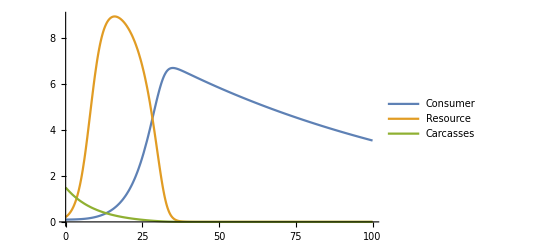

```mathematica
Tend = 100;
NDsolution = NDSolve[Join[sysNDSolve/.partestall, init1],{𝒞[t], H[t], U[t]}, {t, 0, Tmax}];
varst/.First[NDsolution]/.t->Tend
Plot[Evaluate[varst/.NDsolution],{t, 0, Tend}, PlotRange->All, PlotLegends->{"Consumer", "Resource", "Carcasses"}]
```

NDSolve::ndsz: At t == 262.939, step size is effectively zero; singularity or stiff system suspected.

{3.55629,-1.84023×10^-10,3.68675×10^-12}

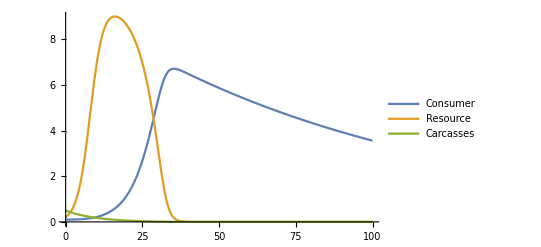

```mathematica
NDsolution = NDSolve[Join[sysNDSolve/.partestall, init2],{𝒞[t], H[t], U[t]}, {t, 0, Tmax}];
varst/.First[NDsolution]/.t->Tend
Plot[Evaluate[varst/.NDsolution],{t, 0, Tend}, PlotRange->All, PlotLegends->{"Consumer", "Resource", "Carcasses"}]
```